# random drum head

Screencast on how it works. (external link)

With n random points in the plane, make a drum head that smoothly goes through them and determine the spectrum

```mathematica
Manipulate[n=5;
pts=RandomReal[{-1,1},{n,2}];
pts=pslider;
fst=FindShortestTour[pts];
ordered=pts[[fst[[2]]]];
ptsrepeat=Join[ordered,ordered[[2;;5]]];
intx=Interpolation[ptsrepeat[[All,1]],Method->"Spline"];
inty=Interpolation[ptsrepeat[[All,2]],Method->"Spline"];
pp=ParametricPlot[{intx[t],inty[t]},{t,3,Length[ptsrepeat]-2},AspectRatio->Automatic],{{pslider,{{0,1},{1,0},{-1,0},{0,-1},{1,1}}},Locator}]
```

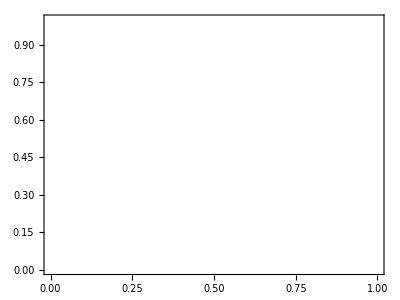

-Graphics-

```mathematica
pppts=pp[[1,1,3,2,1]];
reg=BoundaryMeshRegion[pppts,Line[Range[Length[pppts]]]];
freqs=Sqrt[NDEigenvalues[{-Laplacian[f[x,y],{x,y}],DirichletCondition[f[x,y]==0,True]},{f},{x,y}∈reg,10]];
circlefreqs=Sqrt[NDEigenvalues[{-Laplacian[f[x,y],{x,y}],DirichletCondition[f[x,y]==0,True]},{f},{x,y}∈Disk[{0,0},0.75],10]];
graph=Graphics[Table[InfiniteLine[{freqs[[i]],0},{0,1}],{i,Length[freqs]}],Frame->True,PlotRange->{{0,Max[freqs] 1.1},All}]
circlegraph=Graphics[{Red,InfiniteLine[{#,0},{0,1}]&/@circlefreqs},Frame->True,PlotRange->{{0,Max[freqs] 1.1},All}]
```